```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
ElecData=Import["CompareNewLimit_X10.dat"];(*Cross section has been normalised to 10^-38 cm^2*)
x=ElecData[[All,1]];(*Dark matter mass in MeV*)
sigmaElec=ElecData[[All,2]];(*Cross sec in cm^2 *)
```

```mathematica
ElecTable=Table[{x[[i]],sigmaElec[[i]] 10^-38},{i,Length[x]}];
```

```mathematica
ElecBound=Interpolation[ElecTable,InterpolationOrder->4];
```

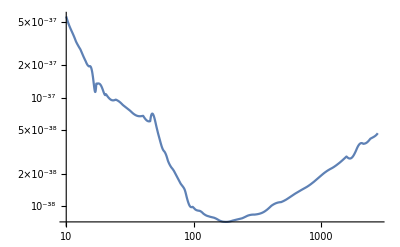

```mathematica
LogLogPlot[ElecBound[x],{x,10,2800}]
```

```mathematica
(************** LT plot *****************************)
```

```mathematica
LTData=Import["LTplot.dat"];
temp=LTData[[All,1]];(*Temp in kelvin*);
Lum=LTData[[All,2]];(* erg s^-1*);
```

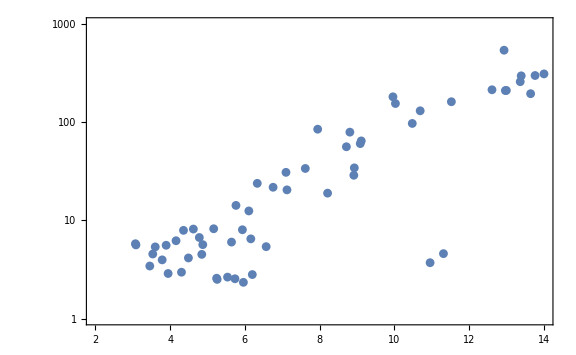

```mathematica
ListLogPlot[LTData,PlotRange->{{2,14},{1,1000}}, Frame->True,ImageSize->Large]
```

```mathematica
(********************** Mass Radius relation for WD ***************************************************)
```

```mathematica
Rsun=7 10^8(*mtr*);
Msun=2 10^30(*kg*);
Mch=1.4 Msun;
μe=2;
Rwd[M_]:=0.0126Rsun (2/μe)^(5/3)(M/Msun)^(-1/3)(1-(M/Mch)^(4/3))^(1/2)(*in mtrs*)
```

```mathematica
Rwd[0.1Msun]
```

1.87184×10^7

```mathematica
Ravg=(Rwd[0.1Msun]+Rwd[1.35Msun])/2.;
```

```mathematica
(*Calculation of Ctot *)
```

```mathematica
(************************** Definitions of Pnτ ***********************************)
Nn[R_,nn_]:=4/3 π R^3 nn
sigmaSat[R_,nn_]:=(π R^2)/Nn[R,nn]
tau[sigma_,R_,nn_]:=(3sigma)/(2sigmaSat[R,nn])
(*pn[sigma_?NumericQ,R_?NumericQ,nn_?NumericQ,N_?NumericQ]:=2/Factorial[N] NIntegrate[y Exp[-y tau[sigma,R,nn]](y tau[sigma,R,nn])^N,{y,0,1},MaxRecursion->12,WorkingPrecision->6,AccuracyGoal-> 4]*)
pn[sigma_?NumericQ,R_?NumericQ,nn_?NumericQ,N_?NumericQ]:=2/(Factorial[N] tau[sigma,R,nn]^2)(Gamma[N+2]-Gamma[N+2,tau[sigma,R,nn]])
```

```mathematica
(* Numerical Values *)
vbar=20.0(*km/sec*);
vtilde=247(*km/sec*);
ηnum=√(3/(2 vbar^2))vtilde;
ρ0=10^4(*GeV/cc*);
Tsun=3 10^17; (*sec*)
fMBboosted[u_,η_,mdm_]:=ρ0/mdm(3/(2 vbar^2))^(3/2)4/(√π)u^2 Exp[-3/(2 vbar^2)u^2](*Exp[-η^2] Sinh[2 (√(3/(2 vbar^2))u) η]/(2(√(3/(2 vbar^2))u) η)*)(*x=√(3/(2 vbar^2))u*)
β[mdm_,mN_]:=(4.0mN mdm)/(mN+mdm)^2
gN[u_,vesc_,N_,mdm_,mN_]:=1/β[mdm,mN] vesc^2/(vesc^2+u^2)((1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1))-(1/β[mdm,mN]-1);
wΩminus[σ_,u_,vesc_,N_,n_,mdm_,mN_]:=σ n (u^2+vesc^2)gN[u,vesc,N,mdm,mN]
umin[vesc_,N_,mdm_,mN_]:=vesc √((1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1)-1)
umax[vesc_,N_,mdm_,mN_]:=vesc Sqrt[(1/(1-β[mdm,mN])(1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1))-1]
```

```mathematica
cctomtrInv=10^6;
mtrtoKm=10^-3;
```

```mathematica
CN[R_?NumericQ,σ_?NumericQ,vesc_?NumericQ,N_?NumericQ,nn_?NumericQ,mdm_?NumericQ,mN_?NumericQ]:= π R^2 pn[σ,R,nn,N]NIntegrate[gN[u,vesc,N,mdm,mN] fMBboosted[u,ηnum,mdm]/u(u^2+vesc^2),{u,umin[vesc,N,mdm,mN],umax[vesc,N,mdm,mN]},MaxRecursion->12,WorkingPrecision->6,AccuracyGoal-> 4](cctomtrInv/ mtrtoKm)
(* UNITS : R in mtr, u in km/sec, vesc in km/sec, mdm in GeV, ρ0 in Gev/cc, σ in m^2 *)
```

```mathematica
Nmax[R_?NumericQ,σ_?NumericQ,vesc_?NumericQ,nn_?NumericQ,mdm_?NumericQ,mn_?NumericQ]:=For[Nobj=1,Nobj≤ 10^5,Nobj++,If[Tsun CN[R,σ,vesc,Nobj,nn,mdm,mn]≤1,Return[Nobj];Break[]]];
```

```mathematica
(*CAUTION : NEEDS to get cleared from the NSUN value before Running*)
Ctot[R_,σ_,vesc_,nn_,mdm_?NumericQ,mn_]:=Sum[CN[R,σ,vesc,n1,nn,mdm,mn],{n1,1,Nmax[R,σ,vesc,nn,mdm,mn]}]
```

```mathematica
(* Temperature of WD and asscociated constraint *)
```

```mathematica
G=6.67408×10^-11 (*m^3 kg^-1 s^-2*);
clight=3 10^8;(*m/sec*)
σ0=5.67 10^-8(*Watt m^-2 k^-4 *);
conversionfactor=6.24 10^9;(*Joule to GeV*)
```

```mathematica
RHSofConstraint[R_,T_,M_]:=4π σ0 R^2 T^4(1-(2G M)/(R clight^2))^2 conversionfactor; (* R in mtr, T in Kelvin, M in Kg *)
```

```mathematica
RHSofConstraint[0.07 10^8,4000,2 10^30]
```

5.57244×10^31

```mathematica
Ctot[0.07 10^8,10^-45,6 10^3,10^36,10^-2,12.0]
```

3.52885×10^33

```mathematica
(*plotElecWD2=ListLogPlot[{Table[{x,(1/10^33 10^x Ctot[0.07 10^8,10^-46,6 10^3,10^40,10^x,0.5 10^-3])^0.25},{x,-3,6,0.5}],Table[{x,(1/10^33 10^x Ctot[0.07 10^8,10^-48,6 10^3,10^40,10^x,0.5 10^-3])^0.25},{x,-3,6,0.5}],Table[{x,(1/10^33 10^x Ctot[0.07 10^8,10^-50,6 10^3,10^40,10^x,0.5 10^-3])^0.25},{x,-3,6,0.5}],Table[{x,1},{x,-3,6,0.5}]},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Dashed,Black}},PlotRange->Full,Frame->True,Joined-> True,AxesOrigin ->{-3,Automatic},FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["T_DM/T_obs",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-46 m^2","σ = 10^-48 m^2","σ = 10^-50 m^2"},Top],PlotLabel->"Scattering with electrons in White Dwarf of 5000K (ρ_DM=10^4 GeV/cc)"]*)
```

```mathematica
(*Export["plotWD2.pdf",plotElecWD2];*)
```

```mathematica
MyRad=Sort[Table[r1=((Lum[[i]]624.15 10^28)/(4π conversionfactor σ0 (temp[[i]]10^3)^4))^0.5,{i,1,Length[temp]}]];
```

```mathematica
WDdatMdm1=Table[{r1=MyRad[[i]],lum1=0.1 Ctot[r1,10^-46,6 10^3,10^40,0.1,0.5 10^-3],Temp=(lum1/(4π σ0 conversionfactor (r1)^2))^0.25},{i,1,Length[temp]}];
```

```mathematica
Export["WDdataM1GeV.dat",WDdatMdm1];
```

```mathematica
T1=WDdatMdm1[[All,3]](*Temp in Kelvin*);
Lum1=WDdatMdm1[[All,2]](*Lum GeV s^-1*);
Table1=Table[{T1[[i]]/1000.,Lum1[[i]]/(624.15 10^28)},{i,Length[T1]}];
```

```mathematica
WDdatMdm2=Table[{r1=MyRad[[i]],lum1=0.1 Ctot[r1,10^-48,6 10^3,10^40,0.1,0.5 10^-3],Temp=(lum1/(4π σ0 conversionfactor (r1)^2))^0.25},{i,1,Length[temp]}];
```

```mathematica
Export["WDdataM100MeV.dat",WDdatMdm2];
```

```mathematica
T2=WDdatMdm2[[All,3]];(*Temp in Kelvin*)
Lum2=WDdatMdm2[[All,2]];(*Lum GeV s^-1*)
Table2=Table[{T2[[i]]/1000.,Lum2[[i]]/(10^28*624.15)},{i,Length[T2]}];
```

```mathematica
(*p1=ListLogPlot[{Table1,Table2},PlotStyle->{{Thick,Blue},{Thick,Red},{Thin,Green}},Joined -> True,PlotRange->{{2,14},{1,10^3}},Frame->True,AxesOrigin ->{Automatic,Automatic},FrameLabel->{Style["T_Eff [10^3 K]",FontSize->20,Bold],Style["L [10^28erg s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-46 m^2","σ = 10^-48 m^2"},Top],PlotLabel->"Scattering with electrons in White Dwarfs (M_DM= 100 MeV, ρ_DM=10^4 GeV/cc)"]*)
```

```mathematica
(*Export["plotWDM4new1.pdf",p1];*)
```

```mathematica
L[DMdens_,Mstar_,sigma_,r_]:=3 10^27(DMdens/50.0)(2 Mstar/Msun)^2(sigma/10^-44)(10^9/r);
```

```mathematica
WDdatMdm3=Table[{r1=MyRad[[i]],lum3=L[50.0,Msun,10^-41,100 r1],Temp=(lum3/(4π σ0 conversionfactor (r1)^2))^0.25},{i,1,Length[temp]}];
T3=WDdatMdm3[[All,3]];(*Temp in Kelvin*)
Lum3=WDdatMdm3[[All,2]];(*Lum GeV s^-1*)
Table3=Table[{T3[[i]]/1000.,Lum3[[i]]/(10^28*624.15)},{i,Length[T3]}];
```

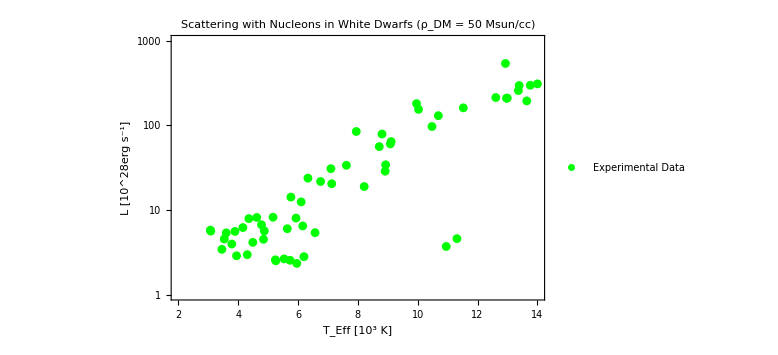

```mathematica
p2=ListLogPlot[LTData,PlotStyle->{{Thin,Green}},PlotRange->{{2,14},{1,10^3}},Frame->True,AxesOrigin ->{Automatic,Automatic},FrameLabel->{Style["T_Eff [10^3 K]",FontSize->20,Bold],Style["L [10^28erg s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"Experimental Data"},Top],PlotLabel->"Scattering with Nucleons in White Dwarfs (ρ_DM = 50 Msun/cc)"]
```

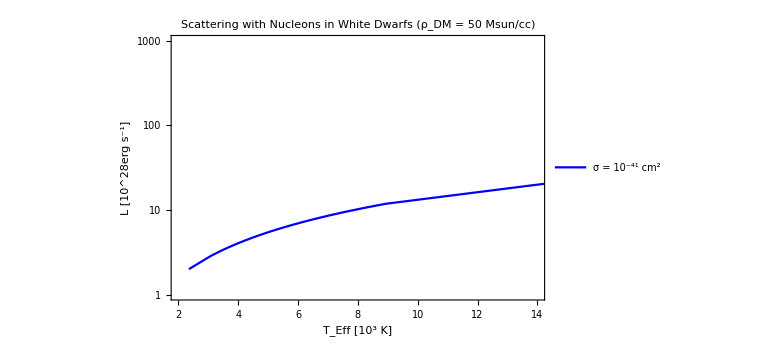

```mathematica
p3=ListLogPlot[Table3,PlotStyle->{{Thick,Blue}},Joined-> True,PlotRange->{{2,14},{1,10^3}},Frame->True,AxesOrigin ->{Automatic,Automatic},FrameLabel->{Style["T_Eff [10^3 K]",FontSize->20,Bold],Style["L [10^28erg s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-41 cm^2"},Top],PlotLabel->"Scattering with Nucleons in White Dwarfs (ρ_DM = 50 Msun/cc)"]
```

```mathematica
(*p4=Show[p1,p2]*)
```

```mathematica
(*Export["plotnew.pdf",p4];*)
```